```mathematica
xValues1 = Range[0, 1.4, 0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4}

```mathematica
{0.,0.1,0.2,0.30000000000000004,0.4,0.5,0.6000000000000001,0.7000000000000001,0.8,0.9,1.,1.1,1.2000000000000002,1.3,1.4}
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4}

```mathematica
yValues1 = {1.0,0.986, 0.956, 0.873, 0.761, 0.579, 0.382, 0.219, 0.011, 0.005, 0.002, 0.0006, 0.0002, 0.0}
```

{1.,0.986,0.956,0.873,0.761,0.579,0.382,0.219,0.011,0.005,0.002,0.0006,0.0002,0.}

```mathematica
data1 = Partition[Riffle[xValues1, yValues1], 2]
```

{{0.,1.},{0.1,0.986},{0.2,0.956},{0.3,0.873},{0.4,0.761},{0.5,0.579},{0.6,0.382},{0.7,0.219},{0.8,0.011},{0.9,0.005},{1.,0.002},{1.1,0.0006},{1.2,0.0002},{1.3,0.}}

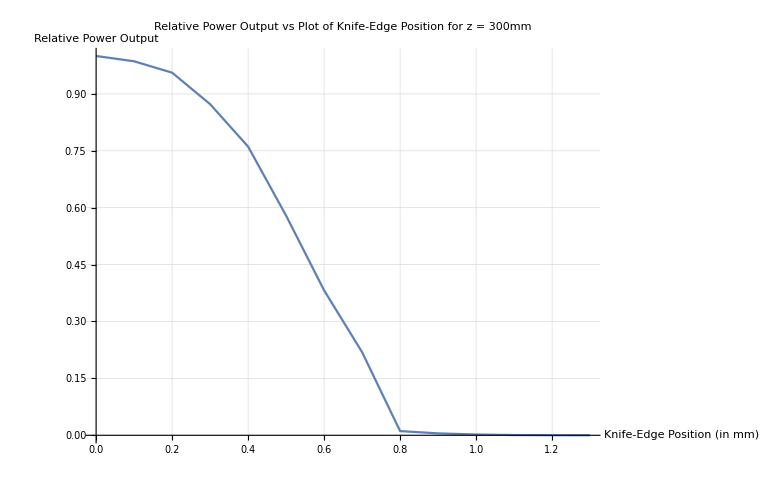

```mathematica
ListPlot[data1, Joined->True, AxesLabel->{"Knife-Edge Position (in mm)", "Relative Power Output"}, PlotLabel->"Relative Power Output vs Plot of Knife-Edge Position for z = 300mm", GridLines->Automatic]
```

```mathematica
xValues2 = Range[0, 1.5, 0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5}

```mathematica
yValues2 = {1.0, 0.984, 0.927, 0.830, 0.676, 0.508, 0.342, 0.196, 0.093, 0.034, 0.013, 0.0061, 0.003, 0.002, 0.0}
```

{1.,0.984,0.927,0.83,0.676,0.508,0.342,0.196,0.093,0.034,0.013,0.0061,0.003,0.002,0.}

```mathematica
data2 = Partition[Riffle[xValues2, yValues2], 2]
```

{{0.,1.},{0.1,0.984},{0.2,0.927},{0.3,0.83},{0.4,0.676},{0.5,0.508},{0.6,0.342},{0.7,0.196},{0.8,0.093},{0.9,0.034},{1.,0.013},{1.1,0.0061},{1.2,0.003},{1.3,0.002},{1.4,0.}}

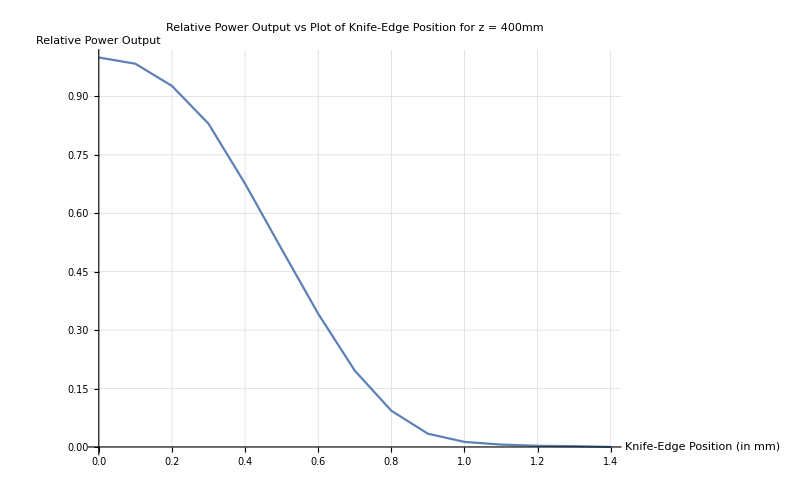

```mathematica
ListPlot[data2, Joined->True, AxesLabel->{"Knife-Edge Position (in mm)", "Relative Power Output"}, PlotLabel->"Relative Power Output vs Plot of Knife-Edge Position for z = 400mm", GridLines->Automatic]
```

```mathematica
xValues3 = Range[0, 1.6, 0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6}

```mathematica
yValues3 = {1.0, 0.986, 0.948, 0.875, 0.756, 0.588, 0.441, 0.286, 0.187, 0.090, 0.028, 0.010, 0.004, 0.002, 0.001, 0.0}
```

{1.,0.986,0.948,0.875,0.756,0.588,0.441,0.286,0.187,0.09,0.028,0.01,0.004,0.002,0.001,0.}

```mathematica
{1.,0.986,0.948,0.875,0.756,0.608,0.471,0.3,0.204,0.09,0.028,0.01,0.004,0.002,0.001,0.}
```

```mathematica
{1.,0.986,0.948,0.865,0.736,0.587,0.471,0.276,0.204,0.09,0.028,0.01,0.004,0.002,0.001,0.}
```

```mathematica
data3 = Partition[Riffle[xValues3, yValues3], 2]
```

{{0.,1.},{0.1,0.986},{0.2,0.948},{0.3,0.875},{0.4,0.756},{0.5,0.588},{0.6,0.441},{0.7,0.286},{0.8,0.187},{0.9,0.09},{1.,0.028},{1.1,0.01},{1.2,0.004},{1.3,0.002},{1.4,0.001},{1.5,0.}}

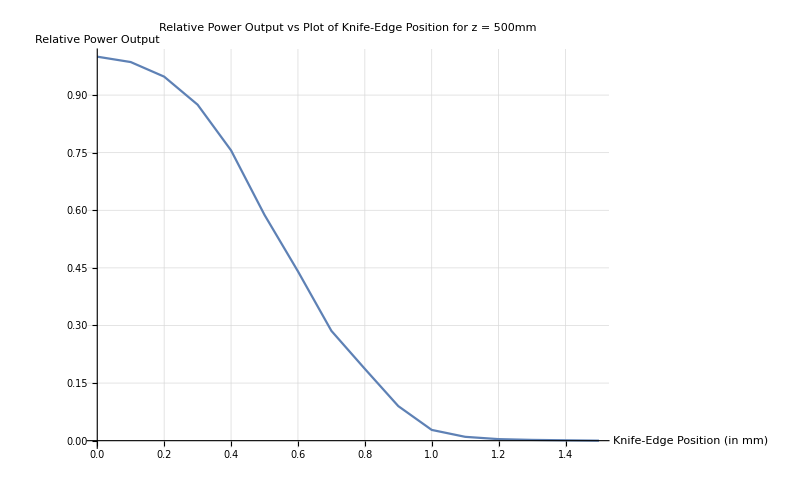

```mathematica
ListPlot[data3, Joined->True, AxesLabel->{"Knife-Edge Position (in mm)", "Relative Power Output"}, PlotLabel->"Relative Power Output vs Plot of Knife-Edge Position for z = 500mm", GridLines->Automatic]
```

```mathematica
temp = Table[4.96 * yValues3[[i]], {i, 1,Length[yValues3]}]
```

{4.96,4.89056,4.70208,4.34,3.74976,2.91648,2.18736,1.41856,0.92752,0.4464,0.13888,0.0496,0.01984,0.00992,0.00496,0.}